#1 Perfect plasticity

```mathematica
Subscript[σ, Y]=3*10^8;
El = 210*10^9;
ep=Subscript[σ, Y]/El;
N[ep]
```

0.00142857

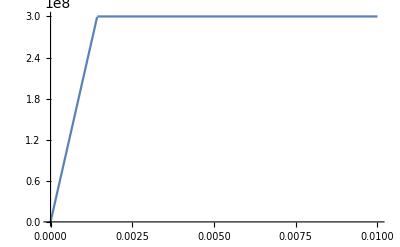

```mathematica
sigma[x_]:=Piecewise[{{El*x, 0<x<ep}, {Subscript[σ, Y], x>ep}}]
Plot[sigma[x],{x,0,0.01}]
```

#2 Isotropic hardening (linear)

```mathematica
??Global`*
```

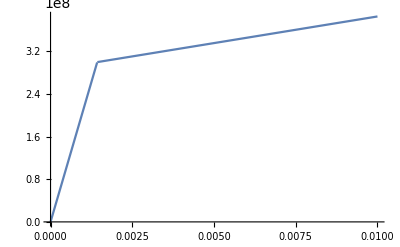

```mathematica
Subscript[σ, Y]=3*10^8;
K=1*10^10;
El = 210*10^9;
ep=Subscript[σ, Y]/El;
Subscript[K, 1][α_]:=Subscript[σ, Y]+K α;
sigma[x_]:=Piecewise[{{El*x, 0<x<ep}, {Subscript[K, 1][x-ep], x>ep}}]
Plot[sigma[x],{x,0,0.01},AxesOrigin->{0,0}]
```

```mathematica
Grid[Table[{i,Subscript[K, 1][i]},{i,0,0.02,0.005}]]
```

0. | 3.×10^8
0.005 | 3.5×10^8
0.01 | 4.×10^8
0.015 | 4.5×10^8
0.02 | 5.×10^8

#3 Alternative isotropic hardening (exponential)

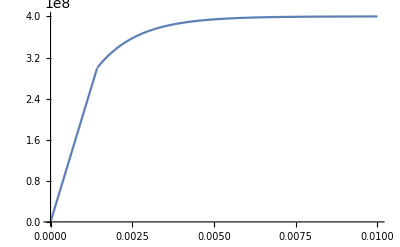

```mathematica
Subscript[σ, Y]=3*10^8;
K=1*10^8; 
H=0;
θ=1;
δ=800;
Subscript[K, 2][α_]:=Subscript[σ, Y]+θ H α+K(1-Exp[-δ α]);
sigma[x_]:=Piecewise[{{El*x, 0<x<ep}, {Subscript[K, 2][x-ep], x>ep}}]
Plot[sigma[x],{x,0,0.01},AxesOrigin->{0,0}]
```

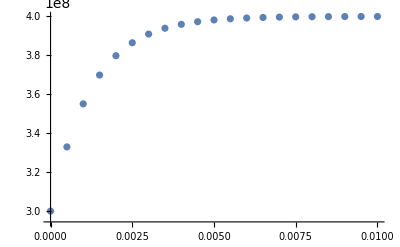

```mathematica
ListPlot[Table[{i,Subscript[K, 2][i]},{i,0,0.01,0.0005}]]
```

```mathematica
Grid[Table[{i,Subscript[K, 2][i]},{i,0,0.01,0.0005}]]
```

0. | 3.×10^8
0.0005 | 3.32968×10^8
0.001 | 3.55067×10^8
0.0015 | 3.69881×10^8
0.002 | 3.7981×10^8
0.0025 | 3.86466×10^8
0.003 | 3.90928×10^8
0.0035 | 3.93919×10^8
0.004 | 3.95924×10^8
0.0045 | 3.97268×10^8
0.005 | 3.98168×10^8
0.0055 | 3.98772×10^8
0.006 | 3.99177×10^8
0.0065 | 3.99448×10^8
0.007 | 3.9963×10^8
0.0075 | 3.99752×10^8
0.008 | 3.99834×10^8
0.0085 | 3.99889×10^8
0.009 | 3.99925×10^8
0.0095 | 3.9995×10^8
0.01 | 3.99966×10^8

#4 Kinematic hardening